```mathematica
Options[FractalTurtleBasic]={PlotStyle -> Thickness[0.01]};
FractalTurtle[rewrite_, start_String, d_Integer, angle_, opts___]:= Module[
{dir = {1,0}, rotLeft, rotRight, style, lastPoint, chars, ang = N[angle Degree], pts},
style = PlotStyle /. {opts} /. Options[FractalTurtleBasic];
If[!ListQ[style], style = {style}];
{rotLeft, rotRight} = RotationTransform /@ ({-1, 1} ang);
chars = Characters[Nest[StringReplace[#, rewrite]&, start, d]];
pts = Reap[
Sow[lastPoint = {0,0}]⟦1⟧;
Do[Which[
c== "+", dir = rotLeft[dir],
c == "-", dir = rotRight[dir],
c == "F", Sow[lastPoint += dir],
c == "B", Sow[lastPoint -= dir],
c == "i", {rotLeft, rotRight} = {rotRight, rotLeft}],
{c, chars}]]⟦2⟧  // First;
Graphics[Append[style, Line[pts]],Sequence@@FilterRules[{opts}, Options[Graphics]], PlotRange->All]
];

FractalTurtleGrid[r_, s_String, depths_List, angle_, opts___]:=
GraphicsGrid[Map[FractalTurtle[r, s, #, angle, opts]&, depths, {Depth[depths]-1}]];
```

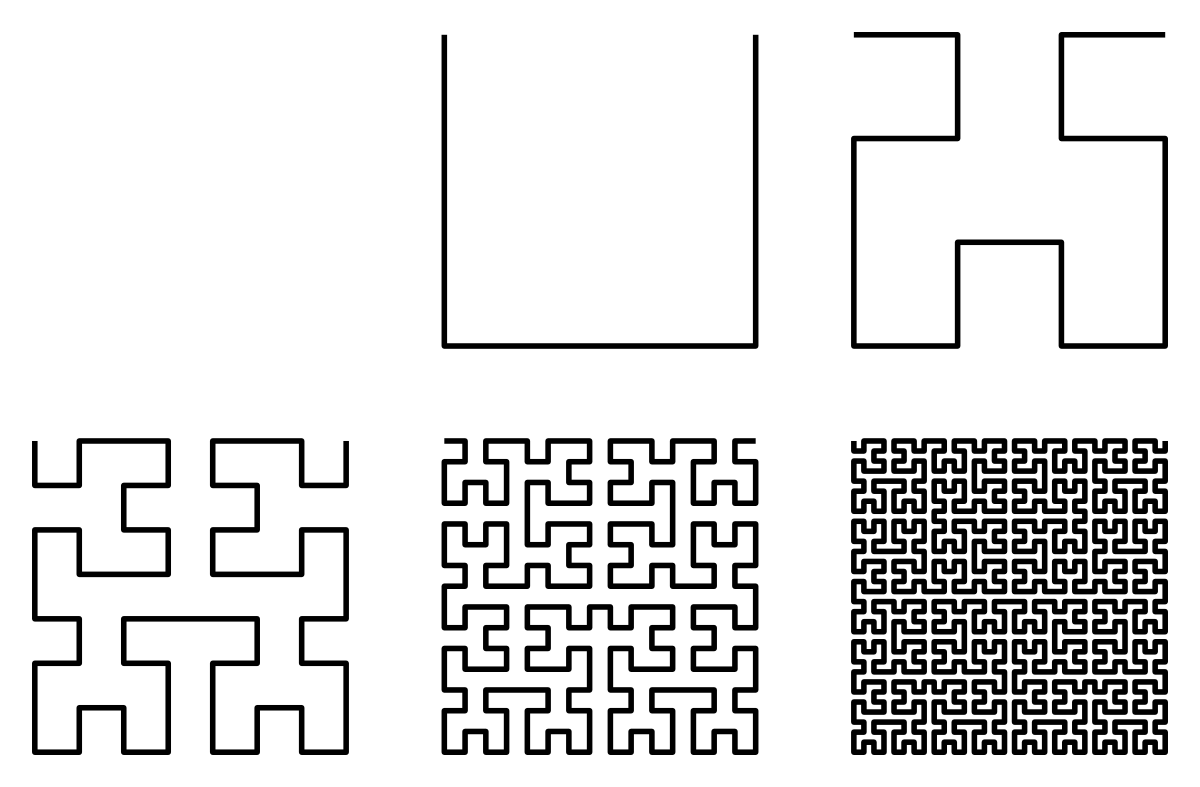

```mathematica
FractalTurtleGrid["X"-> "+iXiF-XFX-FiXi+", "X",{{0,1,2},{3,4,5}}, 90]
```

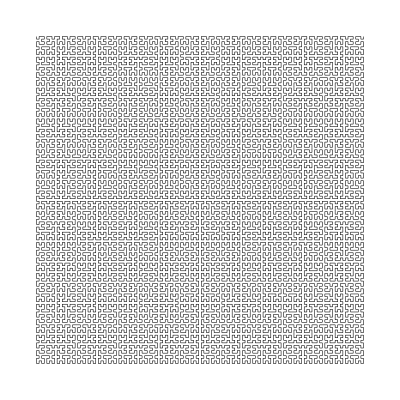

```mathematica
FractalTurtle["X"-> "+iXiF-XFX-FiXi+", "X", 7, 90, PlotStyle-> Thickness[0.001]]
```